# GWMMatch - 03 : Tapering

### 0. Preamble

#### Load Package

```mathematica
<<GWMMatch`
```

### 1. Build a test signal

```mathematica
sampleRate=2048.0;   (*Hz*)
duration=2.0;      (*seconds*)
f0=40.0;     (*starting frequency[Hz]*)
fDot=30.0;     (*frequency sweep rate[Hz/s]*)

nTime=Round[sampleRate*duration];
deltaT=1.0/sampleRate;
deltaF=1.0/duration;
fLow=10.0;   (*lower frequency cutoff[Hz]*)
fHigh=512.0;  (*upper frequency cutoff[Hz]*)

(*A pure sinusoid with a sharp onset—pathological spectral leakage*)
f0=150.0;  (*Hz*)
fdot = 30;
tVals=Table[n*deltaT,{n,0,nTime-1}];
hSharp=Table[Sin[2.0 Pi (f0 + fdot t) t],{t,tVals}];

(*Apply tapers with three different widths*)
hTaperAuto=GWTaper[hSharp];                             (*auto-detect width*)
hTaperFixed=GWTaper[hSharp,"TAPER_STARTEND",200];     (*200 samples each end*)
hTaperStart=GWTaper[hSharp,"TAPER_START"];              (*start only*)

Print["Signal length: ",nTime," samples"];
```

Signal length: 4096 samples

### 2. Time-domain view

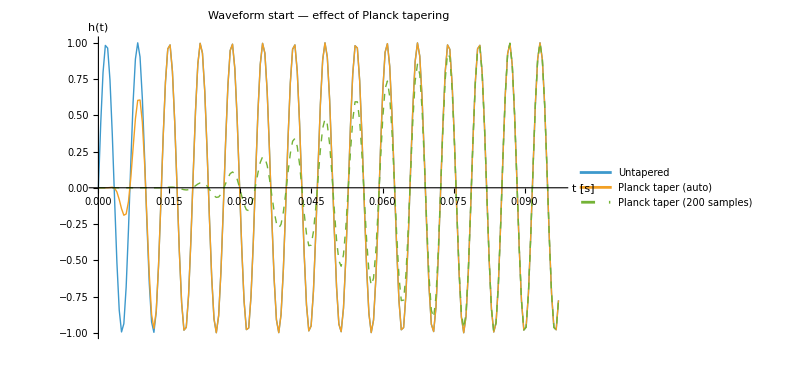

```mathematica
nShow=200;   (*samples to display at each edge*)

plotTimeStart=ListPlot[{Transpose[{tVals[[1;;nShow]],hSharp[[1;;nShow]]}],Transpose[{tVals[[1;;nShow]],hTaperAuto[[1;;nShow]]}],Transpose[{tVals[[1;;nShow]],hTaperFixed[[1;;nShow]]}]},Joined->True,PlotStyle->{{Thick},{Thick},{Thick,Dashed}},PlotLegends->{"Untapered","Planck taper (auto)","Planck taper (200 samples)"},PlotLabel->"Waveform start — effect of Planck tapering",AxesLabel->{"t [s]","h(t)"},PlotRange->All,ImageSize->600]
```

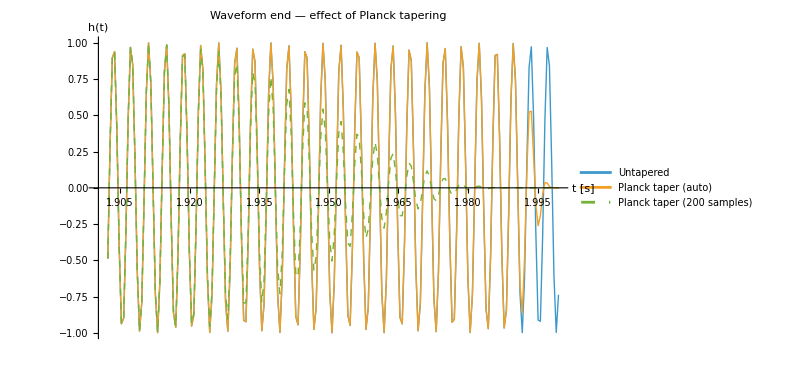

```mathematica
plotTimeEnd=ListPlot[{Transpose[{tVals[[-nShow;;-1]],hSharp[[-nShow;;-1]]}],Transpose[{tVals[[-nShow;;-1]],hTaperAuto[[-nShow;;-1]]}],Transpose[{tVals[[-nShow;;-1]],hTaperFixed[[-nShow;;-1]]}]},Joined->True,PlotStyle->{{Thick},{Thick},{Thick,Dashed}},PlotLegends->{"Untapered","Planck taper (auto)","Planck taper (200 samples)"},PlotLabel->"Waveform end — effect of Planck tapering",AxesLabel->{"t [s]","h(t)"},PlotRange->All,ImageSize->600]
```

### 3. Frequency-domain: spectral leakage

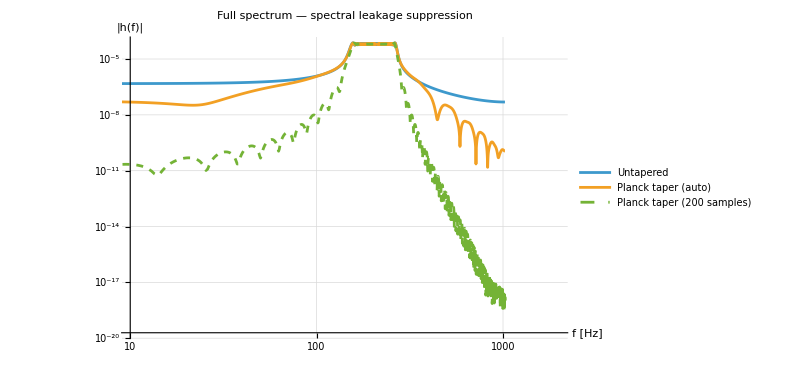

```mathematica
(*Compute one-sided ASDs*)asdOf[h_]:=With[{nF=Floor[nTime/2]+1,fft=GWMMatch`Private`ForwardFFT[h,deltaT]},Transpose[{Table[(k-1)*deltaF,{k,1,nF}],Abs[fft]*2.0*deltaT  (*one-sided ASD,unnormalised*)}]];

asdSharp=asdOf[hSharp];
asdAuto=asdOf[hTaperAuto];
asdFixed=asdOf[hTaperFixed];

plotASDFull=ListLogLogPlot[{asdSharp,asdAuto,asdFixed},Joined->True,PlotStyle->{{Thick},{Thick},{Thick,Dashed}},PlotLegends->{"Untapered","Planck taper (auto)","Planck taper (200 samples)"},PlotLabel->"Full spectrum — spectral leakage suppression",AxesLabel->{"f [Hz]","|h(f)|"},PlotRange->{{10,2000},All},GridLines->Automatic,GridLinesStyle->LightGray,ImageSize->600]
```

The role of the taper is to suppress the power being spread to the higher and lower frequencies.

### 4. Effect of tapering on mismatch

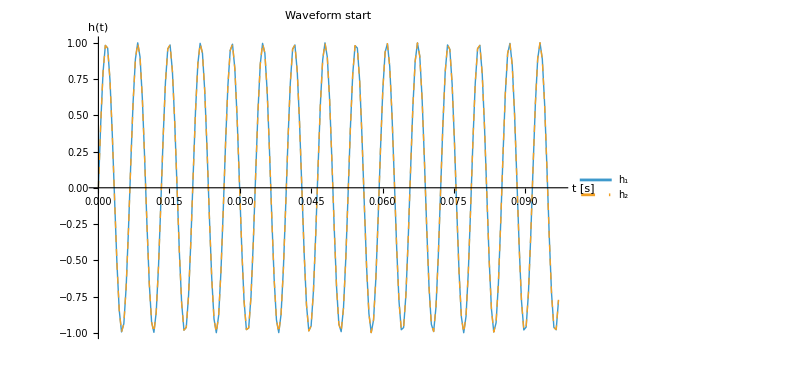

```mathematica
nFreq=Floor[nTime/2]+1;
psdFlat=FlatPSD[nFreq,deltaF,fLow];

(*A slightly different sinusoid at with perturned f and fdot Hz*)
δf = 0.001;
δfdot = 0.1;
hRef=Table[Sin[2.0 Pi ((f0+δf) + (fdot + δfdot) t) t],{t,tVals}];
hRefTapered=GWTaper[hRef];

plotTimeStart=ListPlot[{Transpose[{tVals[[1;;nShow]],hSharp[[1;;nShow]]}],Transpose[{tVals[[1;;nShow]],hRef[[1;;nShow]]}]},Joined->True,PlotStyle->{{Thick},{Thick,Dashed},{Thick,Dashed}},PlotLegends->{"h_1","h_2"},PlotLabel->"Waveform start",AxesLabel->{"t [s]","h(t)"},PlotRange->All,ImageSize->600]
```

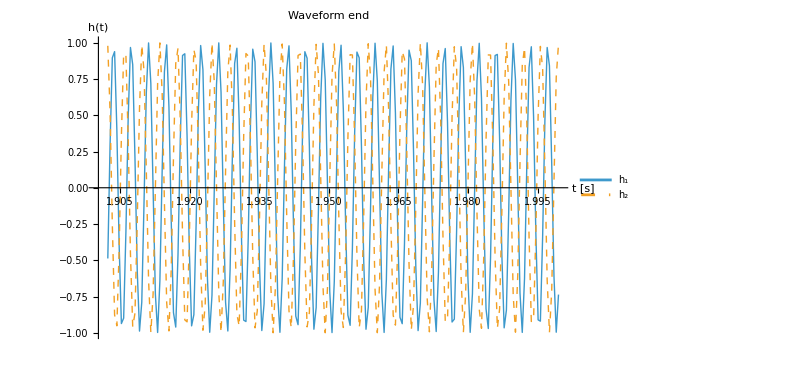

```mathematica
plotTimeEnd=ListPlot[{Transpose[{tVals[[-nShow;;-1]],hSharp[[-nShow;;-1]]}],Transpose[{tVals[[-nShow;;-1]],hRef[[-nShow;;-1]]}]},Joined->True,PlotStyle->{{Thick},{Thick,Dashed}},PlotLegends->{"h_1","h_2"},PlotLabel->"Waveform end",AxesLabel->{"t [s]","h(t)"},PlotRange->All,ImageSize->600]
```

```mathematica
computeMatch[ha_,hb_]:=First[GWOptimizedMatch[ha,hb,deltaT,psdFlat,deltaF,fLow,fHigh]];

Print["\n-- Mismatch between waveforms --"];
Print["  Untapered vs untapered:  ",N[1-computeMatch[hSharp,hRef],6]];
Print["  Both tapered (auto):     ",N[1-computeMatch[hTaperAuto,hRefTapered],6]];
Print["  Both tapered (200 samp): ",N[1-computeMatch[hTaperFixed,GWTaper[hRef,"TAPER_STARTEND",200]],6]];
```

-- Mismatch between waveforms --

Untapered vs untapered:  0.019196

Both tapered (auto):     0.0173535

Both tapered (200 samp): 0.0138666